Final Photon Distribution from Compton Scattering

Notebook: Óscar Amaro, May 2023 @ GoLP-EPP

Introduction
We derive an analytical expression for the final distribution of photons in momenta after Compton scattering against head-on relativistic electrons. The Klein-Nishina formula is used in the boosted frame of the center of mass of the electron. We follow 
The del Gaudio2020 paper might have a typo (β-> -β) when boosting the photon energy to the COM frame.
 https://en.wikipedia.org/wiki/Klein%E2%80%93Nishina_formula
 
 See also the BadialiBilbao2022JPP.ipynb notebook
 
The main idea is dN/dϵp = dN/dθ dθ/dϵp and we write θ as a function of ϵp.
θ - scattering angle from KN cross-section
ϵp - final photon energy in lab frame

## dN/dϵp

```mathematica
Clear[re,λ,λp,λc,dσdΩ,dσdθ,dσdΩ0,ϵ,c,e,ϵeV,dσdΩlow,cdf,getθ,ℏ,ω,dNdϵp,γ,m,ϵ0,β]

dNdθ=(c^2 h^2 re^2 ((mc2 (-1+β) γ ϵp)/(c^2 m (-mc2 γ+ϵp))+(c^2 m (-1+β)^3 γ^3 (mc2 γ-ϵp))/(c^2 m (-1+β) γ (mc2 γ-ϵp)-mc2 ϵp)+(((-1+β) γ ϵ ϵp-mc2 ((-1+β) γ^2 ϵ+ϵp))^2)/(ϵ^2 (-mc2 γ+ϵp)^2)))/(2 (-1+β)^2 γ^2 (c h+(h mc2 ϵp)/(c m (-1+β) γ (-mc2 γ+ϵp)))^2);
dθdϵp=mc2^2/((1+β) ϵ (-mc2 γ+ϵp)^2 √((mc2 ϵp (2 mc2 (1+β) γ^2 ϵ-(mc2+2 (1+β) γ ϵ) ϵp))/((1+β)^2 γ^2 ϵ^2 (-mc2 γ+ϵp)^2)));

((dNdθ dθdϵp)/.{mc2->m c^2})//FullSimplify
```

(c^4 m^2 re^2 (((-1+β)^3 γ^3 (c^2 m γ-ϵp))/((-1+β) γ (c^2 m γ-ϵp)-ϵp)+((-1+β) γ ϵp)/(-c^2 m γ+ϵp)+(((-1+β) γ ϵ ϵp-c^2 m ((-1+β) γ^2 ϵ+ϵp))^2)/(ϵ^2 (-c^2 m γ+ϵp)^2)))/(2 (1+β) ϵ (ϵp+(-1+β) γ (-c^2 m γ+ϵp))^2 √(-(c^2 m ϵp (2 (1+β) γ ϵ ϵp+c^2 m (-2 (1+β) γ^2 ϵ+ϵp)))/((1+β)^2 γ^2 ϵ^2 (-c^2 m γ+ϵp)^2)))

```mathematica
Clear[re,λ,λp,λc,dσdΩ,dσdθ,dσdΩ0,ϵ,c,e,ϵeV,dσdΩlow,cdf,getθ,ℏ,ω,dNdϵp,γ,β,pe,pγ,pγmec,m,ϵ0]
Refine[((c^4 m^2 re^2 (((-1+β)^3 γ^3 (c^2 m γ-ϵp))/((-1+β) γ (c^2 m γ-ϵp)-ϵp)+((-1+β) γ ϵp)/(-c^2 m γ+ϵp)+(((-1+β) γ ϵ ϵp-c^2 m ((-1+β) γ^2 ϵ+ϵp))^2)/(ϵ^2 (-c^2 m γ+ϵp)^2)))/(2 (1+β) ϵ (ϵp+(-1+β) γ (-c^2 m γ+ϵp))^2 √(-(c^2 m ϵp (2 (1+β) γ ϵ ϵp+c^2 m (-2 (1+β) γ^2 ϵ+ϵp)))/((1+β)^2 γ^2 ϵ^2 (-c^2 m γ+ϵp)^2)))/.{m->1/c^2})//Simplify,{β>0,β<1,γ>0,ϵp>0,ϵ>0,γ>ϵp}]//FullSimplify
```

(re^2 γ (γ-ϵp) (((-1+β)^3 γ^3 (γ-ϵp))/((-1+β) γ (γ-ϵp)-ϵp)+((-1+β) γ ϵp)/(-γ+ϵp)+((-1+β) γ ϵ (γ-ϵp)+ϵp)^2/(ϵ^2 (γ-ϵp)^2)))/(2 √(2 (1+β) γ ϵ (γ-ϵp)-ϵp) √ϵp (ϵp+(-1+β) γ (-γ+ϵp))^2)

Real units

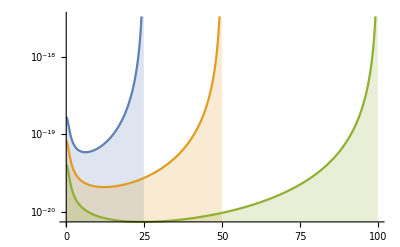

```mathematica
Clear[re,λ,λp,λc,dσdΩ,dσdθ,dσdΩ0,ϵ,c,e,ϵeV,dσdΩlow,cdf,getθ,ℏ,ω,dNdϵp,γ,β,pe,pγ,pγmec,m,ϵ0]
dNdϵp=(c^4 m^2 re^2 (((-1+β)^3 γ^3 (c^2 m γ-ϵp))/((-1+β) γ (c^2 m γ-ϵp)-ϵp)+((-1+β) γ ϵp)/(-c^2 m γ+ϵp)+(((-1+β) γ ϵ ϵp-c^2 m ((-1+β) γ^2 ϵ+ϵp))^2)/(ϵ^2 (-c^2 m γ+ϵp)^2)))/(2 (1+β) ϵ (ϵp+(-1+β) γ (-c^2 m γ+ϵp))^2 √(-(c^2 m ϵp (2 (1+β) γ ϵ ϵp+c^2 m (-2 (1+β) γ^2 ϵ+ϵp)))/((1+β)^2 γ^2 ϵ^2 (-c^2 m γ+ϵp)^2)));

γ=Sqrt[1+(pe/(m c))^2];
β=Sqrt[1-1/γ^2];
ϵ=2.5 m c^2;

Clear[ϵ0,m,c,e,re]
e=1.6 10^-19;
c=3 10^8;
m=9.1 10^-31;
ϵ0=8.854 10^-12;
re=1/(4π ϵ0)e^2/(m c^2);

LogPlot[{(dNdϵp/.{pe->25 m c,ϵp-> m c^2Sqrt[1+(pγmec)^2]}),(dNdϵp/.{pe->50 m c,ϵp-> m c^2Sqrt[1+(pγmec)^2]}),(dNdϵp/.{pe->100 m c,ϵp-> m c^2Sqrt[1+(pγmec)^2]})},{pγmec,0,100},PlotRange->Automatic,Filling->Bottom]
```

Normalized units mc^2=1

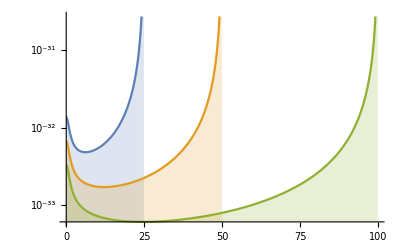

```mathematica
Clear[re,λ,λp,λc,dσdΩ,dσdθ,dσdΩ0,ϵ,c,e,ϵeV,dσdΩlow,cdf,getθ,ℏ,ω,dNdϵp,γ,β,pe,pγ,pγmec,m,ϵ0]
dNdϵp=(re^2 γ (γ-ϵp) (((-1+β)^3 γ^3 (γ-ϵp))/((-1+β) γ (γ-ϵp)-ϵp)+((-1+β) γ ϵp)/(-γ+ϵp)+((-1+β) γ ϵ (γ-ϵp)+ϵp)^2/(ϵ^2 (γ-ϵp)^2)))/(2 √(2 (1+β) γ ϵ (γ-ϵp)-ϵp) √ϵp (ϵp+(-1+β) γ (-γ+ϵp))^2);

γ=Sqrt[1+(pe)^2];
β=Sqrt[1-1/γ^2];
ϵ=2.5;

Clear[ϵ0,m,c,e,re]
e=1.6 10^-19;
c=3 10^8;
m=9.1 10^-31;
ϵ0=8.854 10^-12;
re=1/(4π ϵ0)e^2/(m c^2);

LogPlot[{(dNdϵp/.{pe->25 ,ϵp-> Sqrt[1+(pγmec)^2]}),(dNdϵp/.{pe->50 ,ϵp-> Sqrt[1+(pγmec)^2]}),(dNdϵp/.{pe->100 ,ϵp-> Sqrt[1+(pγmec)^2]})},{pγmec,0,100},PlotRange->Automatic,Filling->Bottom]
```

## dN/dθ

```mathematica
Clear[re,λ,λp,λc,dσdΩ,dσdθ,dσdΩ0,ϵ,c,e,ϵeV,dσdΩlow,cdf,getθ,ℏ,ω]
λp=λ(1+λc/λ(1-Cos[θ])); (*λp = λ', ϵ = λc/λ = Eγ/mc^2*)
dσdΩ=re^2/2(λ/λp)^2(λ/λp+λp/λ-Sin[θ]^2)//FullSimplify
```

(re^2 λ^2 (1+(λc-λc Cos[θ])/λ+λ/(λ+λc-λc Cos[θ])-Sin[θ]^2))/(2 (λ+λc-λc Cos[θ])^2)

(0.0000320256 h^2 (1+(124.95 c m (h/(c m)-(h Cos[θ])/(c m)))/h+(0.0080032 h)/(c m ((1.008 h)/(c m)-(h Cos[θ])/(c m)))-Sin[θ]^2))/(c^2 m^2 ((1.008 h)/(c m)-(h Cos[θ])/(c m))^2)

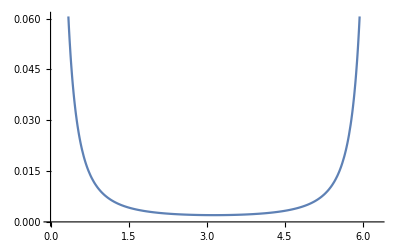

```mathematica
exp=(re^2 λ^2 (1+(λc-λc Cos[θ])/λ+λ/(λ+λc-λc Cos[θ])-Sin[θ]^2))/(2 (λ+λc-λc Cos[θ])^2)//.{λc->h/(m c),re->1,λ->h c/ϵ,ϵ->2.5 m c^2 γ(1+β),β->Sqrt[1-1/γ^2],γ->25}
Plot[exp,{θ,0,2π}]
```

```mathematica
Clear[mc2,ϵOp,ϵO,ϵp,γ,β,ϕ,dNγdθO,CosθO,ϵ,m,c,λc,λ,re]
CosθO=(-((-1+β) γ ϵ ϵp)+mc2 ((-1+β) γ^2 ϵ+ϵp))/((-1+β) γ ϵ (mc2 γ-ϵp));
λc=h/(m c);
Print["dN/θO (ϵp)"]
((re^2 λ^2 (1+(λc-λc CosθO)/λ+λ/(λ+λc-λc CosθO)-(1-CosθO^2)))/(2 (λ+λc-λc CosθO)^2)/.{λ->h c/ϵ})//FullSimplify
```

dN/θO (ϵp)

(c^2 h^2 re^2 ((mc2 (-1+β) γ ϵp)/(c^2 m (-mc2 γ+ϵp))+(c^2 m (-1+β)^3 γ^3 (mc2 γ-ϵp))/(c^2 m (-1+β) γ (mc2 γ-ϵp)-mc2 ϵp)+(((-1+β) γ ϵ ϵp-mc2 ((-1+β) γ^2 ϵ+ϵp))^2)/(ϵ^2 (-mc2 γ+ϵp)^2)))/(2 (-1+β)^2 γ^2 (c h+(h mc2 ϵp)/(c m (-1+β) γ (-mc2 γ+ϵp)))^2)

```mathematica
Clear[mc2,ϵOp,ϵO,ϵp,γ,β,ϕ,dNγdθO,CosθO,ϵ,m,c]
(((c^2 h^2 re^2 ((mc2 (-1+β) γ ϵp)/(c^2 m (-mc2 γ+ϵp))+(c^2 m (-1+β)^3 γ^3 (mc2 γ-ϵp))/(c^2 m (-1+β) γ (mc2 γ-ϵp)-mc2 ϵp)+(((-1+β) γ ϵ ϵp-mc2 ((-1+β) γ^2 ϵ+ϵp))^2)/(ϵ^2 (-mc2 γ+ϵp)^2)))/(2 (-1+β)^2 γ^2 (c h+(h mc2 ϵp)/(c m (-1+β) γ (-mc2 γ+ϵp)))^2))/.{mc2-> m c^2})//FullSimplify
```

(re^2 (((-1+β)^3 γ^3 (c^2 m γ-ϵp))/((-1+β) γ (c^2 m γ-ϵp)-ϵp)+((-1+β) γ ϵp)/(-c^2 m γ+ϵp)+(((-1+β) γ ϵ ϵp-c^2 m ((-1+β) γ^2 ϵ+ϵp))^2)/(ϵ^2 (-c^2 m γ+ϵp)^2)))/(2 (1+γ (-1+β+(c^2 m)/(-c^2 m γ+ϵp)))^2)

## dθ/dϵp

```mathematica
Clear[mc2,ϵOp,ϵO,ϵp,γ,β,ϕ,dNγdθO,ϵpp,ϵ]

ϵO=γ ϵ(1+β);
ϵOp=ϵO mc2/(mc2+ϵO(1-Cos[θO]));
Print["ϵp(θO)"]
ϵpp=γ ϵOp(1-Cos[θO])

Print["D[ϵp,θO]"]
D[ϵpp,θO]//Simplify

Clear[mc2,ϵOp,ϵO,ϵp,γ,β,ϕ,dNγdθO,CosθO]
Print["Cos[θO] = f(ϵp)"]
Solve[(mc2 (1+β) γ^2 ϵ (1-CosθO))/(mc2+(1+β) γ ϵ (1-CosθO))==ϵp,CosθO][[1,1,2]]//FullSimplify

(* dθO/dϵp *)
Clear[mc2,ϵOp,ϵO,ϵp,γ,β,ϕ,dNγdθO,CosθO]
CosθO=(mc2 (1+β) γ^2 ϵ-(mc2+(1+β) γ ϵ) ϵp)/((1+β) γ ϵ (mc2 γ-ϵp));

Print["D[θO,ϵp]=1/D[ϵp,θO]"]
1/((mc2^2 (1+β) γ^2 ϵ Sqrt[1-CosθO^2])/(mc2+(1+β) γ ϵ-(1+β) γ ϵ CosθO)^2)//FullSimplify
```

ϵp(θO)

(mc2 (1+β) γ^2 ϵ (1-Cos[θO]))/(mc2+(1+β) γ ϵ (1-Cos[θO]))

D[ϵp,θO]

(mc2^2 (1+β) γ^2 ϵ Sin[θO])/(mc2+(1+β) γ ϵ-(1+β) γ ϵ Cos[θO])^2

Cos[θO] = f(ϵp)

(mc2 (1+β) γ^2 ϵ-(mc2+(1+β) γ ϵ) ϵp)/((1+β) γ ϵ (mc2 γ-ϵp))

D[θO,ϵp]=1/D[ϵp,θO]

mc2^2/((1+β) ϵ (-mc2 γ+ϵp)^2 √((mc2 ϵp (2 mc2 (1+β) γ^2 ϵ-(mc2+2 (1+β) γ ϵ) ϵp))/((1+β)^2 γ^2 ϵ^2 (-mc2 γ+ϵp)^2)))